A vertical wall of an oven is 60 cm long and is covered with a metal sheet maintained at 170°C. Air temperature inside the oven is 90°C and the pressure is atmospheric. Calculate the local heat-transfer coefficient at the end of the wall and the average heat transfer coefficient over the wall.

```mathematica
Ra = g β (Tw-T0) y^3 / (ν α);
```

```mathematica
η = x Ra^(1/4) / y;
```

```mathematica
ψ = α Ra^(1/4) f[η];
```

```mathematica
u = D[ψ,y];
```

```mathematica
v = -D[ψ,x];
```

```mathematica
T = T0+(Tw-T0)θ[η];
```

```mathematica
momEqn = u D[v,x]+v D[v,y] == ν D[v,{x,2}]+ g β (T-T0) // (FullSimplify[#]&) // (#[[1]][[5]]&) // (#/.ν->α Pr&) //(Collect[#,α]&) // (#[[2]]&)
```

4 Pr θ[(x ((g (-T0+Tw) y^3 β)/(Pr α^2))^(1/4))/y]-2 f'[(x ((g (-T0+Tw) y^3 β)/(Pr α^2))^(1/4))/y]^2+3 f[(x ((g (-T0+Tw) y^3 β)/(Pr α^2))^(1/4))/y] f''[(x ((g (-T0+Tw) y^3 β)/(Pr α^2))^(1/4))/y]-4 Pr f^(3)[(x ((g (-T0+Tw) y^3 β)/(Pr α^2))^(1/4))/y]

```mathematica
egyEqn = u D[T,x]+v D[T,y]== α D[T,{x,2}]  // (FullSimplify[#]&) // (#[[1]][[5]]&)
```

3 f[(x ((g (-T0+Tw) y^3 β)/(α ν))^(1/4))/y] θ'[(x ((g (-T0+Tw) y^3 β)/(α ν))^(1/4))/y]-4 θ''[(x ((g (-T0+Tw) y^3 β)/(α ν))^(1/4))/y]

```mathematica
momAsgn = {θ[η/.ν->α Pr]->θt[ηt],
f[η/. ν->α Pr]->ft[ηt],
f'[η /. ν->α Pr]-> ft'[ηt],
f''[η /. ν->α Pr]-> ft''[ηt],
f'''[η /. ν->α Pr]-> ft'''[ηt]};
```

```mathematica
momEqnFinal = momEqn /. momAsgn
```

4 Pr θt[ηt]-2 ft'[ηt]^2+3 ft[ηt] ft''[ηt]-4 Pr ft^(3)[ηt]

```mathematica
egyAsgn = {f[η]->ft[ηt],
θ'[η]->θt'[ηt],
θ''[η]->θt''[ηt]};
```

```mathematica
egyEqnFinal = egyEqn /. egyAsgn
```

3 ft[ηt] θt'[ηt]-4 θt''[ηt]

```mathematica
θp0[Prt_]:= Module[{fval},
sol = NDSolve[{momEqnFinal==0,egyEqnFinal==0,
ft[0]==0,ft'[0]==0,θt[0]==1,ft'[10]==0,θt[10]==0} /. Pr->Prt,
{ft,θt},{ηt,0,10}];
fval=sol[[1]][[2]][[2]]'[0.0]];
solVal[Prt_] := Module[{sol},
sol = NDSolve[{momEqnFinal==0,egyEqnFinal==0,
ft[0]==0,ft'[0]==0,θt[0]==1,ft'[10]==0,θt[10]==0} /. Pr->Prt,
{ft,θt},{ηt,0,10}]];
```

```mathematica
airProps = Import["/Users/durgaprasadpydi/Documents/deliverables/reviews_and_reports/ta_duty/2025_jul_nov/Prasad131.github.io/slides/assets/air_props.csv"];
```

```mathematica
{"Temp (°C)","ρ (kg/m.b3)","cp (kJ/kg·K)","k (W/m·K)","β (×10.b3 1/K)","μ (×10⁻⁵ kg/m·s)","ν (×10⁶ m.b2/s)","α (×10⁶ m.b2/s)","Pr"}
airProps[[2;;,5]] = airProps[[2;;,5]] 10^-3;
airProps[[2;;,7]] = airProps[[2;;,7]]10^-6;
airProps[[2;;,8]] = airProps[[2;;,8]]10^-6;
```

{Temp (°C),ρ (kg/m.b3),cp (kJ/kg·K),k (W/m·K),β (×10.b3 1/K),μ (×10⁻⁵ kg/m·s),ν (×10⁶ m.b2/s),α (×10⁶ m.b2/s),Pr}

```mathematica
νI = Interpolation[airProps[[2;;,{1,7}]]];
βI = Interpolation[airProps[[2;;,{1,5}]] ];
PrI = Interpolation[airProps[[2;;,{1,9}]]];
αI = Interpolation[airProps[[2;;,{1,8}]]];
κI = Interpolation[airProps[[2;;,{1,4}]]];
```

```mathematica
TFilm = 0.5 (170+90);
problem = {g->9.81,β->βI[TFilm],Tw->170,T0->90,
ν->νI[TFilm],α->αI[TFilm],κ->κI[TFilm],θ'[η]-> θp0[PrI[TFilm]]};
```

```mathematica
hY= (-κ D[T,x]/(Tw-T0))/. problem
```

(2.71936 (y^3)^(1/4))/y

```mathematica
hLocal = hY /. y->0.6
```

3.08979

```mathematica
hMean = (Integrate[hY,{y,0,0.6}]/y) /. y->0.6
```

4.11972

Evaluating the velocity components also

```mathematica
sol = solVal[PrI[TFilm]]
```

{{ft→InterpolatingFunction[…],θt→InterpolatingFunction[…]}}

```mathematica
vSol = v /. {f[η]->ft[ηt],f'[η]->ft'[ηt]} // (#/.sol&) // (#/.ηt->η&)//(#/.problem&)
```

{-(1.67785 √(y^3) InterpolatingFunction[…][(210.059 x (y^3)^(1/4))/y])/y}

```mathematica
vSolL = vSol /. y->0.6
```

{-1.29965 InterpolatingFunction[…][238.673 x]}

```mathematica
δ = 10 y Ra^(-1/4) /. Join[problem,{y->0.6}]
```

0.0418983

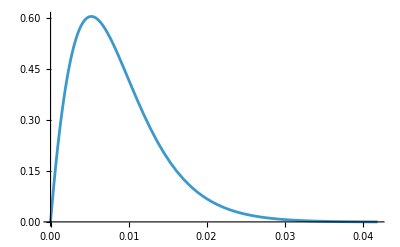

```mathematica
Plot[Evaluate[vSolL],{x,0,δ}]
```

```mathematica
vMax = NMaxValue[{vSolL[[1]],0<=x<=δ},{x}]
```

0.604744